# Ball balancing robot

```mathematica
ClearAll["Global`*"]
```

## Braccio 1

Posizione del giunto sferico (x1, y1, z1)

```mathematica
s1=Simplify[Solve[{
α x1+γ (z1-h)==0,
L^2==x1^2+(h-z1)^2},{x1,z1}]][[1]]
```

{x1→(L^2 α γ)/(√(L^2 α^2 (α^2+γ^2))),z1→h-(L^2 α^2)/(√(L^2 α^2 (α^2+γ^2)))}

```mathematica
x1=Abs[(L^2 α γ)/(√(L^2 α^2 (α^2+γ^2)))];
y1=0;
z1=h-(L^2 α^2)/(√(L^2 α^2 (α^2+γ^2)))*Abs[α γ]/(α γ);
```

posizione del gomito (xp,yp,zp)

```mathematica
s2=Simplify[Solve[{
(xp-b)^2+yp^2+zp^2==l^2,
(xp-x11)^2+(yp-y11)^2+(zp-z11)^2==l^2,
yp==0
},{xp,yp,zp}]][[2]]
```

{xp→(b^3-b^2 x11-b x11^2+x11^3-b y11^2+x11 y11^2+b z11^2+x11 z11^2+√(-z11^2 (b^4-4 b^3 x11-4 l^2 (x11^2+z11^2)+(x11^2+y11^2+z11^2)^2-4 b x11 (-2 l^2+x11^2+y11^2+z11^2)+2 b^2 (-2 l^2+3 x11^2+y11^2+z11^2))))/(2 (b^2-2 b x11+x11^2+z11^2)),yp→0,zp→1/(2 z11 (b^2-2 b x11+x11^2+z11^2))(b^2 z11^2-2 b x11 z11^2+x11^2 z11^2+y11^2 z11^2+z11^4+b √(-z11^2 (b^4-4 b^3 x11-4 l^2 (x11^2+z11^2)+(x11^2+y11^2+z11^2)^2-4 b x11 (-2 l^2+x11^2+y11^2+z11^2)+2 b^2 (-2 l^2+3 x11^2+y11^2+z11^2)))-x11 √(-z11^2 (b^4-4 b^3 x11-4 l^2 (x11^2+z11^2)+(x11^2+y11^2+z11^2)^2-4 b x11 (-2 l^2+x11^2+y11^2+z11^2)+2 b^2 (-2 l^2+3 x11^2+y11^2+z11^2))))}

```mathematica
xp=xp/.s2;yp=yp/.s2;zp=zp/.s2;
```

```mathematica
θ11=ArcCos[(xp-b)/l]
```

ArcCos[(-b+(b^3-b^2 x11-b x11^2+x11^3-b y11^2+x11 y11^2+b z11^2+x11 z11^2+√(-z11^2 (b^4-4 b^3 x11-4 l^2 (x11^2+z11^2)+(x11^2+y11^2+z11^2)^2-4 b x11 (-2 l^2+x11^2+y11^2+z11^2)+2 b^2 (-2 l^2+3 x11^2+y11^2+z11^2))))/(2 (b^2-2 b x11+x11^2+z11^2)))/l]

## Braccio 2

```mathematica
s3=FullSimplify[Solve[{α*X2+β*Y2+γ(Z2-h)==0,
(√3)/2*X2+Y2/2==0,
L^2==X2^2+Y2^2+(h-Z2)^2
},{X2,Y2,Z2}]]
```

{{X2→(γ √(L^2 (α^8-8 √3 α^7 β-216 √3 α β^5 (β^2+γ^2)-24 √3 α^5 β (7 β^2+γ^2)+4 α^6 (21 β^2+γ^2)+27 β^6 (3 β^2+4 γ^2)-24 √3 α^3 β^3 (21 β^2+10 γ^2)+90 α^4 (7 β^4+2 β^2 γ^2)+108 α^2 (7 β^6+5 β^4 γ^2))))/((α-√3 β) (α^4-4 √3 α^3 β+9 β^4+12 β^2 γ^2-4 √3 α β (3 β^2+2 γ^2)+2 α^2 (9 β^2+2 γ^2))),Y2→-(√3 γ √(L^2 (α^8-8 √3 α^7 β-216 √3 α β^5 (β^2+γ^2)-24 √3 α^5 β (7 β^2+γ^2)+4 α^6 (21 β^2+γ^2)+27 β^6 (3 β^2+4 γ^2)-24 √3 α^3 β^3 (21 β^2+10 γ^2)+90 α^4 (7 β^4+2 β^2 γ^2)+108 α^2 (7 β^6+5 β^4 γ^2))))/((α-√3 β) (α^4-4 √3 α^3 β+9 β^4+12 β^2 γ^2-4 √3 α β (3 β^2+2 γ^2)+2 α^2 (9 β^2+2 γ^2))),Z2→h-(√(L^2 (α^8-8 √3 α^7 β-216 √3 α β^5 (β^2+γ^2)-24 √3 α^5 β (7 β^2+γ^2)+4 α^6 (21 β^2+γ^2)+27 β^6 (3 β^2+4 γ^2)-24 √3 α^3 β^3 (21 β^2+10 γ^2)+90 α^4 (7 β^4+2 β^2 γ^2)+108 α^2 (7 β^6+5 β^4 γ^2))))/(α^4-4 √3 α^3 β+9 β^4+12 β^2 γ^2-4 √3 α β (3 β^2+2 γ^2)+2 α^2 (9 β^2+2 γ^2))},{X2→-(γ √(L^2 (α^8-8 √3 α^7 β-216 √3 α β^5 (β^2+γ^2)-24 √3 α^5 β (7 β^2+γ^2)+4 α^6 (21 β^2+γ^2)+27 β^6 (3 β^2+4 γ^2)-24 √3 α^3 β^3 (21 β^2+10 γ^2)+90 α^4 (7 β^4+2 β^2 γ^2)+108 α^2 (7 β^6+5 β^4 γ^2))))/((α-√3 β) (α^4-4 √3 α^3 β+9 β^4+12 β^2 γ^2-4 √3 α β (3 β^2+2 γ^2)+2 α^2 (9 β^2+2 γ^2))),Y2→(√3 γ √(L^2 (α^8-8 √3 α^7 β-216 √3 α β^5 (β^2+γ^2)-24 √3 α^5 β (7 β^2+γ^2)+4 α^6 (21 β^2+γ^2)+27 β^6 (3 β^2+4 γ^2)-24 √3 α^3 β^3 (21 β^2+10 γ^2)+90 α^4 (7 β^4+2 β^2 γ^2)+108 α^2 (7 β^6+5 β^4 γ^2))))/((α-√3 β) (α^4-4 √3 α^3 β+9 β^4+12 β^2 γ^2-4 √3 α β (3 β^2+2 γ^2)+2 α^2 (9 β^2+2 γ^2))),Z2→h+(√(L^2 (α^8-8 √3 α^7 β-216 √3 α β^5 (β^2+γ^2)-24 √3 α^5 β (7 β^2+γ^2)+4 α^6 (21 β^2+γ^2)+27 β^6 (3 β^2+4 γ^2)-24 √3 α^3 β^3 (21 β^2+10 γ^2)+90 α^4 (7 β^4+2 β^2 γ^2)+108 α^2 (7 β^6+5 β^4 γ^2))))/(α^4-4 √3 α^3 β+9 β^4+12 β^2 γ^2-4 √3 α β (3 β^2+2 γ^2)+2 α^2 (9 β^2+2 γ^2))}}

```mathematica
X2=-Abs[-((γ √(L^2 (α^8-8 √3 α^7 β-216 √3 α β^5 (β^2+γ^2)-24 √3 α^5 β (7 β^2+γ^2)+4 α^6 (21 β^2+γ^2)+27 β^6 (3 β^2+4 γ^2)-24 √3 α^3 β^3 (21 β^2+10 γ^2)+90 α^4 (7 β^4+2 β^2 γ^2)+108 α^2 (7 β^6+5 β^4 γ^2))))/((α-√3 β) (α^4-4 √3 α^3 β+9 β^4+12 β^2 γ^2-4 √3 α β (3 β^2+2 γ^2)+2 α^2 (9 β^2+2 γ^2))))];
Y2=Abs[Y2/.s3[[2]]];
Z2=h-(√(L^2 (α^8-8 √3 α^7 β-216 √3 α β^5 (β^2+γ^2)-24 √3 α^5 β (7 β^2+γ^2)+4 α^6 (21 β^2+γ^2)+27 β^6 (3 β^2+4 γ^2)-24 √3 α^3 β^3 (21 β^2+10 γ^2)+90 α^4 (7 β^4+2 β^2 γ^2)+108 α^2 (7 β^6+5 β^4 γ^2))))/(α^4-4 √3 α^3 β+9 β^4+12 β^2 γ^2-4 √3 α β (3 β^2+2 γ^2)+2 α^2 (9 β^2+2 γ^2))*(Abs[X2]/(X2/.s3[[2]]));
```

Posizione del gomito x2p,y2p,x2p

```mathematica
s4=FullSimplify[Simplify[Solve[{
(x2p+b*Cos[π/3])^2+(y2p-b*Sin[π/3])^2+z2p^2==l^2,
(x2p-X22)^2+(y2p-Y22)^2+(z2p-Z22)^2==l^2,
(√3)/2 x2p+y2p/2==0
},{x2p,y2p,z2p}]]][[1]]
```

{x2p→(-((2 b+X22-√3 Y22) (b^2-X22^2-Y22^2))+(-2 b+X22-√3 Y22) Z22^2-2 √(-Z22^2 (b^4+2 b^3 (X22-√3 Y22)+(X22^2+Y22^2+Z22^2)^2+2 b (X22-√3 Y22) (-2 l^2+X22^2+Y22^2+Z22^2)+b^2 (-4 l^2+3 X22^2-2 √3 X22 Y22+5 Y22^2+2 Z22^2)-l^2 (X22^2-2 √3 X22 Y22+3 Y22^2+4 Z22^2))))/(2 (4 b^2+X22^2-2 √3 X22 Y22+3 Y22^2+4 b (X22-√3 Y22)+4 Z22^2)),y2p→((2 √3 b+√3 X22-3 Y22) (b^2-X22^2-Y22^2)+(2 √3 b-√3 X22+3 Y22) Z22^2+2 √3 √(-Z22^2 (b^4+2 b^3 (X22-√3 Y22)+(X22^2+Y22^2+Z22^2)^2+2 b (X22-√3 Y22) (-2 l^2+X22^2+Y22^2+Z22^2)+b^2 (-4 l^2+3 X22^2-2 √3 X22 Y22+5 Y22^2+2 Z22^2)-l^2 (X22^2-2 √3 X22 Y22+3 Y22^2+4 Z22^2))))/(2 (4 b^2+X22^2-2 √3 X22 Y22+3 Y22^2+4 b (X22-√3 Y22)+4 Z22^2)),z2p→(2 (b^2+X22^2+Y22^2+b (X22-√3 Y22)) Z22^2+2 Z22^4+2 b √(-Z22^2 (b^4+2 b^3 (X22-√3 Y22)+(X22^2+Y22^2+Z22^2)^2+2 b (X22-√3 Y22) (-2 l^2+X22^2+Y22^2+Z22^2)+b^2 (-4 l^2+3 X22^2-2 √3 X22 Y22+5 Y22^2+2 Z22^2)-l^2 (X22^2-2 √3 X22 Y22+3 Y22^2+4 Z22^2)))+X22 √(-Z22^2 (b^4+2 b^3 (X22-√3 Y22)+(X22^2+Y22^2+Z22^2)^2+2 b (X22-√3 Y22) (-2 l^2+X22^2+Y22^2+Z22^2)+b^2 (-4 l^2+3 X22^2-2 √3 X22 Y22+5 Y22^2+2 Z22^2)-l^2 (X22^2-2 √3 X22 Y22+3 Y22^2+4 Z22^2)))-√3 Y22 √(-Z22^2 (b^4+2 b^3 (X22-√3 Y22)+(X22^2+Y22^2+Z22^2)^2+2 b (X22-√3 Y22) (-2 l^2+X22^2+Y22^2+Z22^2)+b^2 (-4 l^2+3 X22^2-2 √3 X22 Y22+5 Y22^2+2 Z22^2)-l^2 (X22^2-2 √3 X22 Y22+3 Y22^2+4 Z22^2))))/(Z22 (4 b^2+X22^2-2 √3 X22 Y22+3 Y22^2+4 b (X22-√3 Y22)+4 Z22^2))}

```mathematica
x2p=x2p/.s4;y2p=y2p/.s4;z2p=z2p/.s4;
```

```mathematica
θ22=Simplify[ArcCos[(√(x2p^2+y2p^2)-b)/l]]
```

ArcCos[1/l(-b+1/2 √((((2 b+X22-√3 Y22) (b^2-X22^2-Y22^2)+(2 b-X22+√3 Y22) Z22^2+2 √(-Z22^2 (b^4+2 b^3 (X22-√3 Y22)+(X22^2+Y22^2+Z22^2)^2+2 b (X22-√3 Y22) (-2 l^2+X22^2+Y22^2+Z22^2)+b^2 (-4 l^2+3 X22^2-2 √3 X22 Y22+5 Y22^2+2 Z22^2)-l^2 (X22^2-2 √3 X22 Y22+3 Y22^2+4 Z22^2))))^2+((2 √3 b+√3 X22-3 Y22) (b^2-X22^2-Y22^2)+(2 √3 b-√3 X22+3 Y22) Z22^2+2 √3 √(-Z22^2 (b^4+2 b^3 (X22-√3 Y22)+(X22^2+Y22^2+Z22^2)^2+2 b (X22-√3 Y22) (-2 l^2+X22^2+Y22^2+Z22^2)+b^2 (-4 l^2+3 X22^2-2 √3 X22 Y22+5 Y22^2+2 Z22^2)-l^2 (X22^2-2 √3 X22 Y22+3 Y22^2+4 Z22^2))))^2)/(4 b^2+X22^2-2 √3 X22 Y22+3 Y22^2+4 b (X22-√3 Y22)+4 Z22^2)^2))]

## Braccio 3

```mathematica
s5=FullSimplify[Solve[{α*x3+β*y3+γ(z3-h)==0,
(√3)/2*x3-y3/2==0,
L^2==x3^2+y3^2+(h-z3)^2
},{x3,y3,z3}]][[2]]
```

{x3→-(γ √(L^2 (α^8+8 √3 α^7 β+216 √3 α β^5 (β^2+γ^2)+24 √3 α^5 β (7 β^2+γ^2)+4 α^6 (21 β^2+γ^2)+27 β^6 (3 β^2+4 γ^2)+24 √3 α^3 β^3 (21 β^2+10 γ^2)+90 α^4 (7 β^4+2 β^2 γ^2)+108 α^2 (7 β^6+5 β^4 γ^2))))/((α+√3 β) (α^4+4 √3 α^3 β+9 β^4+12 β^2 γ^2+4 √3 α β (3 β^2+2 γ^2)+2 α^2 (9 β^2+2 γ^2))),y3→-(√3 γ √(L^2 (α^8+8 √3 α^7 β+216 √3 α β^5 (β^2+γ^2)+24 √3 α^5 β (7 β^2+γ^2)+4 α^6 (21 β^2+γ^2)+27 β^6 (3 β^2+4 γ^2)+24 √3 α^3 β^3 (21 β^2+10 γ^2)+90 α^4 (7 β^4+2 β^2 γ^2)+108 α^2 (7 β^6+5 β^4 γ^2))))/((α+√3 β) (α^4+4 √3 α^3 β+9 β^4+12 β^2 γ^2+4 √3 α β (3 β^2+2 γ^2)+2 α^2 (9 β^2+2 γ^2))),z3→h+(√(L^2 (α^8+8 √3 α^7 β+216 √3 α β^5 (β^2+γ^2)+24 √3 α^5 β (7 β^2+γ^2)+4 α^6 (21 β^2+γ^2)+27 β^6 (3 β^2+4 γ^2)+24 √3 α^3 β^3 (21 β^2+10 γ^2)+90 α^4 (7 β^4+2 β^2 γ^2)+108 α^2 (7 β^6+5 β^4 γ^2))))/(α^4+4 √3 α^3 β+9 β^4+12 β^2 γ^2+4 √3 α β (3 β^2+2 γ^2)+2 α^2 (9 β^2+2 γ^2))}

```mathematica
x3=-Abs[x3/.s5];
y3=-Abs[y3/.s5];
z3=h-(√(L^2 (α^8+8 √3 α^7 β+216 √3 α β^5 (β^2+γ^2)+24 √3 α^5 β (7 β^2+γ^2)+4 α^6 (21 β^2+γ^2)+27 β^6 (3 β^2+4 γ^2)+24 √3 α^3 β^3 (21 β^2+10 γ^2)+90 α^4 (7 β^4+2 β^2 γ^2)+108 α^2 (7 β^6+5 β^4 γ^2))))/(α^4+4 √3 α^3 β+9 β^4+12 β^2 γ^2+4 √3 α β (3 β^2+2 γ^2)+2 α^2 (9 β^2+2 γ^2))*(Abs[x3]/(x3/.s5));
```

```mathematica
CForm[h-(√(L^2 (α^8+8 √3 α^7 β+216 √3 α β^5 (β^2+γ^2)+24 √3 α^5 β (7 β^2+γ^2)+4 α^6 (21 β^2+γ^2)+27 β^6 (3 β^2+4 γ^2)+24 √3 α^3 β^3 (21 β^2+10 γ^2)+90 α^4 (7 β^4+2 β^2 γ^2)+108 α^2 (7 β^6+5 β^4 γ^2))))/(α^4+4 √3 α^3 β+9 β^4+12 β^2 γ^2+4 √3 α β (3 β^2+2 γ^2)+2 α^2 (9 β^2+2 γ^2))]
```

h - Sqrt(Power(L,2)*(Power(α,8) + 8*Sqrt(3)*Power(α,7)*β + 216*Sqrt(3)*α*Power(β,5)*(Power(β,2) + Power(γ,2)) + 24*Sqrt(3)*Power(α,5)*β*(7*Power(β,2) + Power(γ,2)) + 4*Power(α,6)*(21*Power(β,2) + Power(γ,2)) + 
        27*Power(β,6)*(3*Power(β,2) + 4*Power(γ,2)) + 24*Sqrt(3)*Power(α,3)*Power(β,3)*(21*Power(β,2) + 10*Power(γ,2)) + 90*Power(α,4)*(7*Power(β,4) + 2*Power(β,2)*Power(γ,2)) + 
        108*Power(α,2)*(7*Power(β,6) + 5*Power(β,4)*Power(γ,2))))/
    (Power(α,4) + 4*Sqrt(3)*Power(α,3)*β + 9*Power(β,4) + 12*Power(β,2)*Power(γ,2) + 4*Sqrt(3)*α*β*(3*Power(β,2) + 2*Power(γ,2)) + 2*Power(α,2)*(9*Power(β,2) + 2*Power(γ,2)))

Posizione  del  gomito  x3p, y3p, z3p

```mathematica
s6=FullSimplify[Simplify[Solve[{
(x3p+b*Cos[π/3])^2+(y3p+b*Sin[π/3])^2+z3p^2==l^2,
(x3p-x33)^2+(y3p-y33)^2+(z3p-z33)^2==l^2,
(√3)/2 x3p-y3p/2==0
},{x3p,y3p,z3p}]]][[1]]
```

{x3p→(-((2 b+x33+√3 y33) (b^2-x33^2-y33^2))+(-2 b+x33+√3 y33) z33^2-2 √(-z33^2 (b^4+2 b^3 (x33+√3 y33)+(x33^2+y33^2+z33^2)^2+2 b (x33+√3 y33) (-2 l^2+x33^2+y33^2+z33^2)+b^2 (-4 l^2+3 x33^2+2 √3 x33 y33+5 y33^2+2 z33^2)-l^2 (x33^2+2 √3 x33 y33+3 y33^2+4 z33^2))))/(2 (4 b^2+x33^2+2 √3 x33 y33+3 y33^2+4 b (x33+√3 y33)+4 z33^2)),y3p→(-((2 √3 b+√3 x33+3 y33) (b^2-x33^2-y33^2))+(-2 √3 b+√3 x33+3 y33) z33^2-2 √3 √(-z33^2 (b^4+2 b^3 (x33+√3 y33)+(x33^2+y33^2+z33^2)^2+2 b (x33+√3 y33) (-2 l^2+x33^2+y33^2+z33^2)+b^2 (-4 l^2+3 x33^2+2 √3 x33 y33+5 y33^2+2 z33^2)-l^2 (x33^2+2 √3 x33 y33+3 y33^2+4 z33^2))))/(2 (4 b^2+x33^2+2 √3 x33 y33+3 y33^2+4 b (x33+√3 y33)+4 z33^2)),z3p→(2 (b^2+x33^2+y33^2+b (x33+√3 y33)) z33^2+2 z33^4+2 b √(-z33^2 (b^4+2 b^3 (x33+√3 y33)+(x33^2+y33^2+z33^2)^2+2 b (x33+√3 y33) (-2 l^2+x33^2+y33^2+z33^2)+b^2 (-4 l^2+3 x33^2+2 √3 x33 y33+5 y33^2+2 z33^2)-l^2 (x33^2+2 √3 x33 y33+3 y33^2+4 z33^2)))+x33 √(-z33^2 (b^4+2 b^3 (x33+√3 y33)+(x33^2+y33^2+z33^2)^2+2 b (x33+√3 y33) (-2 l^2+x33^2+y33^2+z33^2)+b^2 (-4 l^2+3 x33^2+2 √3 x33 y33+5 y33^2+2 z33^2)-l^2 (x33^2+2 √3 x33 y33+3 y33^2+4 z33^2)))+√3 y33 √(-z33^2 (b^4+2 b^3 (x33+√3 y33)+(x33^2+y33^2+z33^2)^2+2 b (x33+√3 y33) (-2 l^2+x33^2+y33^2+z33^2)+b^2 (-4 l^2+3 x33^2+2 √3 x33 y33+5 y33^2+2 z33^2)-l^2 (x33^2+2 √3 x33 y33+3 y33^2+4 z33^2))))/(z33 (4 b^2+x33^2+2 √3 x33 y33+3 y33^2+4 b (x33+√3 y33)+4 z33^2))}

```mathematica
x3p=x3p/.s6;y3p=y3p/.s6;z3p=z3p/.s6;
```

```mathematica
θ33=Simplify[ArcCos[(√(x3p^2+y3p^2)-b)/l]]
```

ArcCos[1/l(-b+1/2 √((((2 b+x33+√3 y33) (b^2-x33^2-y33^2)-(-2 b+x33+√3 y33) z33^2+2 √(-z33^2 (b^4+2 b^3 (x33+√3 y33)+(x33^2+y33^2+z33^2)^2+2 b (x33+√3 y33) (-2 l^2+x33^2+y33^2+z33^2)+b^2 (-4 l^2+3 x33^2+2 √3 x33 y33+5 y33^2+2 z33^2)-l^2 (x33^2+2 √3 x33 y33+3 y33^2+4 z33^2))))^2+((2 √3 b+√3 x33+3 y33) (b^2-x33^2-y33^2)+(2 √3 b-√3 x33-3 y33) z33^2+2 √3 √(-z33^2 (b^4+2 b^3 (x33+√3 y33)+(x33^2+y33^2+z33^2)^2+2 b (x33+√3 y33) (-2 l^2+x33^2+y33^2+z33^2)+b^2 (-4 l^2+3 x33^2+2 √3 x33 y33+5 y33^2+2 z33^2)-l^2 (x33^2+2 √3 x33 y33+3 y33^2+4 z33^2))))^2)/(4 b^2+x33^2+2 √3 x33 y33+3 y33^2+4 b (x33+√3 y33)+4 z33^2)^2))]

## Grafico 2

```mathematica
Simplify[Solve[{
γ*Tan[θx]==α,
γ*Tan[θy]==β,
√(α^2+β^2+γ^2)==1
},{α,β,γ}]]
```

{{α→-Tan[θx]/(√(Sec[θy]^2+Tan[θx]^2)),β→-Tan[θy]/(√(Sec[θy]^2+Tan[θx]^2)),γ→-1/(√(Sec[θy]^2+Tan[θx]^2))},{α→Tan[θx]/(√(Sec[θy]^2+Tan[θx]^2)),β→Tan[θy]/(√(Sec[θy]^2+Tan[θx]^2)),γ→1/(√(Sec[θy]^2+Tan[θx]^2))}}

Giunti sferici

```mathematica
parametri:={b->90,l->80,L->117.7,α->-Tan[θx]/(√(Sec[θy]^2+Tan[θx]^2)),β->-Tan[θy]/(√(Sec[θy]^2+Tan[θx]^2)),γ->-1/(√(Sec[θy]^2+Tan[θx]^2))};
```

```mathematica
x1P[tx_,ty_,H_]:=x1/.parametri/.θx->tx/.θy->ty/.h->H
z1P[tx_,ty_,H_]:=z1/.parametri/.θx->tx/.θy->ty/.h->H
x2P[tx_,ty_,H_]:=X2/.parametri/.θx->tx/.θy->ty/.h->H
y2P[tx_,ty_,H_]:=Y2/.parametri/.θx->tx/.θy->ty/.h->H
z2P[tx_,ty_,H_]:=Z2/.parametri/.θx->tx/.θy->ty/.h->H
x3P[tx_,ty_,H_]:=x3/.parametri/.θx->tx/.θy->ty/.h->H
y3P[tx_,ty_,H_]:=y3/.parametri/.θx->tx/.θy->ty/.h->H
z3P[tx_,ty_,H_]:=z3/.parametri/.θx->tx/.θy->ty/.h->H
```

gomiti

```mathematica
zpP[tx_,ty_,H_]:=zp/.x11->x1/.y11->y1/.z11->z1/.parametri/.θx->tx/.θy->ty/.h->H
xpP[tx_,ty_,H_]:=xp/.x11->x1/.y11->y1/.z11->z1/.parametri/.θx->tx/.θy->ty/.h->H
x2pP[tx_,ty_,H_]:=x2p/.X22->X2/.Y22->Y2/.Z22->Z2/.parametri/.θx->tx/.θy->ty/.h->H
y2pP[tx_,ty_,H_]:=y2p/.X22->X2/.Y22->Y2/.Z22->Z2/.parametri/.θx->tx/.θy->ty/.h->H
z2pP[tx_,ty_,H_]:=z2p/.X22->X2/.Y22->Y2/.Z22->Z2/.parametri/.θx->tx/.θy->ty/.h->H
x3pP[tx_,ty_,H_]:=x3p/.x33->x3/.y33->y3/.z33->z3/.parametri/.θx->tx/.θy->ty/.h->H
y3pP[tx_,ty_,H_]:=y3p/.x33->x3/.y33->y3/.z33->z3/.parametri/.θx->tx/.θy->ty/.h->H
z3pP[tx_,ty_,H_]:=z3p/.x33->x3/.y33->y3/.z33->z3/.parametri/.θx->tx/.θy->ty/.h->H
```

```mathematica
th11[tx_,ty_,H_]:=θ11/.x11->x1/.y11->y1/.z11->z1/.parametri/.θx->tx/.θy->ty/.h->H
th22[tx_,ty_,H_]:=θ22/.X22->X2/.Y22->Y2/.Z22->Z2/.parametri/.θx->tx/.θy->ty/.h->H
th33[tx_,ty_,H_]:=θ33/.x33->x3/.y33->y3/.z33->z3/.parametri/.θx->tx/.θy->ty/.h->H
```

```mathematica
Manipulate[Graphics3D[
 {
  PointSize[Large],
(*Braccio 1*)
  Blue, Point[{0, 0, H}],
  Red, Point[{90, 0, 0}],
  Green, Point[{xpP[tx,ty,H], 0, zpP[tx,ty,H] }],
  Black, Point[{x1P[tx,ty,H],0,z1P[tx,ty,H]}],
Line[{{0, 0, H},{x1P[tx,ty,H],0,z1P[tx,ty,H]}}],
Line[{{x1P[tx,ty,H],0,z1P[tx,ty,H]},{xpP[tx,ty,H], 0, zpP[tx,ty,H] }}],
Line[{{90, 0, 0},{xpP[tx,ty,H], 0, zpP[tx,ty,H] }}],
(*Braccio 2*)
Black,Point[{x2P[tx,ty,H],y2P[tx,ty,H],z2P[tx,ty,H]}],
Line[{{0, 0, H},{x2P[tx,ty,H],y2P[tx,ty,H],z2P[tx,ty,H]}}],
Line[{{x1P[tx,ty,H],0,z1P[tx,ty,H]},{x2P[tx,ty,H],y2P[tx,ty,H],z2P[tx,ty,H]}}],
Line[{{x2pP[tx,ty,H],y2pP[tx,ty,H],z2pP[tx,ty,H]},{x2P[tx,ty,H],y2P[tx,ty,H],z2P[tx,ty,H]}}],
Line[{{x2pP[tx,ty,H],y2pP[tx,ty,H],z2pP[tx,ty,H]},{-90*Cos[π/3], 90*Sin[π/3], 0}}],
Red, Point[{-90*Cos[π/3], 90*Sin[π/3], 0}],
Green, Point[{x2pP[tx,ty,H],y2pP[tx,ty,H],z2pP[tx,ty,H]}],
(*Braccio 3*)
Black,Point[{x3P[tx,ty,H],y3P[tx,ty,H],z3P[tx,ty,H]}],
Line[{{0, 0, H},{x3P[tx,ty,H],y3P[tx,ty,H],z3P[tx,ty,H]}}],
Line[{{x3P[tx,ty,H],y3P[tx,ty,H],z3P[tx,ty,H]},{x2P[tx,ty,H],y2P[tx,ty,H],z2P[tx,ty,H]}}],
Line[{{x3P[tx,ty,H],y3P[tx,ty,H],z3P[tx,ty,H]},{x1P[tx,ty,H],0,z1P[tx,ty,H]}}],
Line[{{x3P[tx,ty,H],y3P[tx,ty,H],z3P[tx,ty,H]},{x3pP[tx,ty,H],y3pP[tx,ty,H],z3pP[tx,ty,H]}}],
Line[{{-90*Cos[π/3], -90*Sin[π/3], 0},{x3pP[tx,ty,H],y3pP[tx,ty,H],z3pP[tx,ty,H]}}],
Red, Point[{-90*Cos[π/3], -90*Sin[π/3], 0}],
Green, Point[{x3pP[tx,ty,H],y3pP[tx,ty,H],z3pP[tx,ty,H]}],
Black,Text[th11[tx,ty,H]]
  },
 Axes -> True,
 AxesOrigin -> {0, 0, 0},
PlotRange->{{-200,200},{-200,200},{0,200}},
ImageSize -> {700,600}
],{{tx,-0.1},-1,1},{{ty,-0.1},-1,1},{{H,100},60,200}]
```

## Workspace

### Point cloud

```mathematica
log= OpenAppend["log_BBR2.txt"];
```

```mathematica
write=Function[val,
(*Controllo che non ci siano valori complessi*)
real=True;
For[m=1,m<=Length[val],m++,
If[RealValuedNumberQ[val[[m]]],0,real=False];
If[val[[7]]<0 Or val[[8]]<0 Or val[[9]]<0,real=False,0];
];
If[real==True,
WriteString[log,
FortranForm[val[[1]]],",",
FortranForm[val[[2]]],",",
FortranForm[val[[3]]],",",
FortranForm[val[[4]]],",",
FortranForm[val[[5]]],",",
FortranForm[val[[6]]],"\n"]
];
];
```

```mathematica
θ1[tx_,ty_,H_]:=θ11/.x11->x1/.y11->y1/.z11->z1/.parametri/.θx->tx/.θy->ty/.h->H;
θ2[tx_,ty_,H_]:=θ22/.X22->X2/.Y22->Y2/.Z22->Z2/.parametri/.θx->tx/.θy->ty/.h->H
θ3[tx_,ty_,H_]:=θ33/.x33->x3/.y33->y3/.z33->z3/.parametri/.θx->tx/.θy->ty/.h->H
```

```mathematica
WriteString[log,"thx,thy,h,θ1,θ2,θ3,z1,z2,z3 \n"];
MaxVal=30;
Monitor[
For[i=0,i<=MaxVal,i++,
For[j=0,j<=MaxVal,j++,
For[k=0,k<=MaxVal,k++,
thx=1/MaxVal*i-0.5+0.0001;
thy=1/MaxVal*j-0.5+0.0001;
hh=95/MaxVal*k+60;
Clear[sol];
sol={θ1[tx,ty,H],θ2[tx,ty,H],θ3[tx,ty,H],zpP[tx,ty,H],z2pP[tx,ty,H],z3pP[tx,ty,H]}/.{tx->thx,ty->thy,H->hh};
If[ValueQ[sol],write[{thx,thy,hh,sol[[1]],sol[[2]],sol[[3]],sol[[4]],sol[[5]],sol[[6]]}],0];
]]],{i,j,k}]
```

```mathematica
Close[log]
```

log_BBR2.txt

```mathematica
PointCloud=Import["C:\\Users\\feder\\log_BBR2.csv"];
```

```mathematica
Points=Transpose[{PointCloud[[All,1]],PointCloud[[All,2]],PointCloud[[All,3]]}];
```

### Limit plane equations

PlaneEquations

x=-0.3 y=0.47 z=120
x=0.5 y=0.066 z=120
x=0 y=0 z=150

```mathematica
p1=Solve[{a*-0.3+b*0.47+c*120+d==0,a*0.5+b*0.066+c*120+d==0,a*0+b*0+c*150+d==0},{a,b,c}];
plane1[x_,y_]:=Solve[Simplify[(a*x+b*y+c*z+d)/d/.p1]==0,z][[1,1,2]];
```

x=-0.3 y=-0.47 z=120
x=0.5 y=-0.066 z=120
x=0 y=0 z=150

```mathematica
p2=Solve[{a*-0.3+b*-0.47+c*120+d==0,a*0.5+b*-0.066+c*120+d==0,a*0+b*0+c*150+d==0},{a,b,c}];
plane2[x_,y_]:=Solve[Simplify[(a*x+b*y+c*z+d)/d/.p2]==0,z][[1,1,2]];
```

x = -0.3 y = 0.47 z = 120
x = -0.3 y = -0.47 z = 120
x = 0 y = 0 z = 150

```mathematica
p3=Solve[{a*-0.3+b*0.47+c*120+d==0,a*-0.3+b*-0.47+c*120+d==0,a*0+b*0+c*150+d==0},{a,b,c}];
plane3[x_,y_]:=Solve[Simplify[(a*x+b*y+c*z+d)/d/.p3]==0,z][[1,1,2]];
```

```mathematica
Show[
Graphics3D[{Blue,PointSize[Medium],Point[Points]},Axes->True,AxesLabel->{"θx","θy","h"},ImageSize -> 600,PlotRange->{{-0.6,0.6},{-0.6,0.6},{60,160}},BoxRatios->{1,1,1},SphericalRegion->True],
Plot3D[plane1[x,y],{x,-0.6,0.6},{y,-0.6,0.6},Mesh->None,PlotStyle->{Opacity[0.4],Red}],
Plot3D[plane2[x,y],{x,-0.6,0.6},{y,-0.6,0.6},Mesh->None,PlotStyle->{Opacity[0.4],Green}],
Plot3D[plane3[x,y],{x,-0.6,0.6},{y,-0.6,0.6},Mesh->None,PlotStyle->{Opacity[0.4],Cyan}]
]
```

-Graphics3D-

```mathematica
plane1[θx,θy]
```

-150. (-1.+0.317111 θx+0.627943 θy)

```mathematica
plane2[θx,θy]
```

-150. (-1.+0.317111 θx-0.627943 θy)

```mathematica
plane3[θx,θy]
```

-150. (-1.-0.666667 θx)

```mathematica
h==-150. (-1.+0.3171114599686028 θx+0.6279434850863422 θy)
```

h==-150. (-1.+0.317111 θx+0.627943 θy)

### 2D workspace

```mathematica
line1=Solve[{0.47==m1*-0.3+q1,0.066==m1*0.5+q1},{m1,q1}]
```

{{m1→-0.505,q1→0.3185}}

```mathematica
line2=Solve[{-0.47==m2*-0.3+q2,-0.066==m2*0.5+q2},{m2,q2}]
```

{{m2→0.505,q2→-0.3185}}

```mathematica
Solve[yp==-1/m1*xp+q3,q3]
```

{{q3→(xp+m1 yp)/m1}}

```mathematica
y==-1/m1*x+(xp+m1 yp)/m1
```

y==-x/m1+(xp+m1 yp)/m1

```mathematica
Solve[-1/m1*x+(xp+m1 yp)/m1==m1*x+q1,x]
```

{{x→(-m1 q1+xp+m1 yp)/(1+m1^2)}}

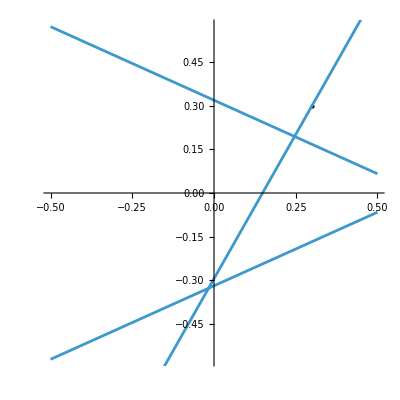

```mathematica
Show[
Plot[{m1*x+q1,y=m2*x+q2}/.line1/.line2,{x,-0.5,0.5},AspectRatio->1],
Graphics[Point[{0.3,0.3}]],
Plot[{-1/m1*x+(0.3+m1 0.3)/m1}/.line1,{x,-0.5,0.5}]
]
```

# V2 - metodo biral

## Useful functions

```mathematica
translate = Function[{x,y,z},
({{1, 0, 0, x}, {0, 1, 0, y}, {0, 0, 1, z}, {0, 0, 0, 1}})
];
```

```mathematica
rotate=Function[{axis,θ},
If[axis=="X",R=({{1, 0, 0, 0}, {0, Cos[θ], -Sin[θ], 0}, {0, Sin[θ], Cos[θ], 0}, {0, 0, 0, 1}}),
If[axis=="Y",R=({{Cos[θ], 0, Sin[θ], 0}, {0, 1, 0, 0}, {-Sin[θ], 0, Cos[θ], 0}, {0, 0, 0, 1}}),
If[axis=="Z",R=({{Cos[θ], -Sin[θ], 0, 0}, {Sin[θ], Cos[θ], 0, 0}, {0, 0, 1, 0}, {0, 0, 0, 1}}),0]]];
R];
```

Get the coordinates of the reference frame RF in respect to ground

```mathematica
getPoint=Function[RF,
{RF[[1,4]],RF[[2,4]],RF[[3,4]]}
];
```

```mathematica
invFrame=Function[RF,
rm=Transpose[RF[[1;;3,1;;3]]];
po=-rm.RF[[1;;3,4]];
({{rm[[1,1]], rm[[1,2]], rm[[1,3]], po[[1]]}, {rm[[2,1]], rm[[2,2]], rm[[2,3]], po[[2]]}, {rm[[3,1]], rm[[3,2]], rm[[3,3]], po[[3]]}, {0, 0, 0, 1}})
];
```

Function to get the rotation matrix of a certain transformation matrix

```mathematica
getRotation=Function[RF,
({{RF[[1,1]], RF[[1,2]], RF[[1,3]]}, {RF[[2,1]], RF[[2,2]], RF[[2,3]]}, {RF[[3,1]], RF[[3,2]], RF[[3,3]]}})
];
```

## Inverse Kinematic

```mathematica
data:={b->90,l->80,Lp->117.7}; (*mm*)
```

Platform reference frame

```mathematica
TP0=translate[x[t],y[t],h[t]].rotate["X",θx[t]].rotate["Y",θy[t]].rotate["Z",θz[t]];
MatrixForm[TP0]
```

(Cos[θy[t]] Cos[θz[t]] | -Cos[θy[t]] Sin[θz[t]] | Sin[θy[t]] | x[t]
Cos[θz[t]] Sin[θx[t]] Sin[θy[t]]+Cos[θx[t]] Sin[θz[t]] | Cos[θx[t]] Cos[θz[t]]-Sin[θx[t]] Sin[θy[t]] Sin[θz[t]] | -Cos[θy[t]] Sin[θx[t]] | y[t]
-Cos[θx[t]] Cos[θz[t]] Sin[θy[t]]+Sin[θx[t]] Sin[θz[t]] | Cos[θz[t]] Sin[θx[t]]+Cos[θx[t]] Sin[θy[t]] Sin[θz[t]] | Cos[θx[t]] Cos[θy[t]] | h[t]
0 | 0 | 0 | 1)

Reference frame for the three vertices

```mathematica
TP1=TP0.translate[Lp,0,0];
TP2=TP0.rotate["Z",4π/6].translate[Lp,0,0];
TP3=TP0.rotate["Z",-4π/6].translate[Lp,0,0];
```

Reference frame of the base points

```mathematica
TBP1=translate[b,0,0];
TBP2=rotate["Z",4π/6].translate[b,0,0];
TBP3=rotate["Z",-4π/6].translate[b,0,0];
```

Reference frame of the revolute joints

```mathematica
TJP1=TBP1.rotate["Y",θ1[t]].translate[l,0,0];
TJP2=TBP2.rotate["Y",θ2[t]].translate[l,0,0];
TJP3=TBP3.rotate["Y",θ3[t]].translate[l,0,0];
```

Reference frame of the ball joints

```mathematica
TBJ1=TJP1.rotate["Y",θJ1[t]].translate[l,0,0];
TBJ2=TJP2.rotate["Y",θJ2[t]].translate[l,0,0];
TBJ3=TJP3.rotate["Y",θJ3[t]].translate[l,0,0];
```

## Solution

Imposing contact between the ball joints and the vertices of the platform

sol = Solve[{getPoint[TBJ1] == getPoint[TP1], getPoint[TBJ2] == getPoint[TP2], getPoint[TBJ3] == getPoint[TP3],
   -1 < θ1[t] < 0, -1 < θ2[t] < 0, -1 < θ3[t] < 0, -3 < θJ1[t] < -1, -3 < θJ2[t] < -1, -3 < θJ3[t] < -1,
   70 < h[t] < 100, -0.3 < θx[t] < 0.3, -0.3 < θy[t] < 0.3
   }, {θ1[t], θJ1[t], θ2[t], θJ2[t], θ3[t], θJ3[t], x[t], y[t], θz[t]}]

$Aborted

```mathematica
Points = {getPoint[TP0],getPoint[TP1],getPoint[TP2],getPoint[TP3],getPoint[TBP1],getPoint[TBP2],getPoint[TBP3],getPoint[TJP1],getPoint[TJP2],getPoint[TJP3],getPoint[TBJ1],getPoint[TBJ2],getPoint[TBJ3]};
Manipulate[
Graphics3D[{
Red,PointSize[Large],Point[Points/.data/.{θx[t]->θX,θy[t]->θY,θz[t]->θZ,x[t]->X,y[t]->Y,h[t]->H,θ1[t]->th1,θ2[t]->th2,θ3[t]->th3,θJ1[t]->thJ1,θJ2[t]->thJ2,θJ3[t]->thJ3}]
},Axes->True,AxesLabel->{"X","Y","Z"},Boxed->True,PlotRange->{{-200,200},{-200,200},{-0.01,200}},ImageSize -> 600],{{θX,0},-1,1},{{θY,0},-1,1},{{θZ,0},-1,1},{{X,0},-100,100},{{Y,0},-100,100},{{H,70},0,140},{{th1,0},-1,0},{{th2,0},-1,0},{{th3,0},-1,0},{{thJ1,-2},-3,0},{{thJ2,-2},-3,0},{{thJ3,-2},-3,0}]
```

ReplaceAll::reps: {data} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

```mathematica
log= OpenAppend["log_BBR.txt"];
```

```mathematica
write=Function[val,
(*Controllo che non ci siano valori complessi*)
real=True;
For[m=1,m<=Length[val],m++,
If[RealValuedNumberQ[val[[m]]],0,real=False]];
If[real==True,
WriteString[log,
FortranForm[val[[1]]],",",
FortranForm[val[[2]]],",",
FortranForm[val[[3]]],",",
FortranForm[val[[4]]],",",
FortranForm[val[[5]]],",",
FortranForm[val[[6]]],",",
 FortranForm[val[[7]]],",",
 FortranForm[val[[8]]],",",
 FortranForm[val[[9]]],",",
 FortranForm[val[[10]]],",",
 FortranForm[val[[11]]],",",
FortranForm[val[[12]]],"\n"]
];
real
];
```

θx=[-0.4,0-4] θy=[-0.4,0-4]  h=[70,140]

```mathematica
WriteString[log,"thx,thy,h,th1,thJ1,th2,thJ2,th3,thJ3,x,y,thz \n"];
MaxVal=10;
For[i=0,i<=MaxVal,i++,
For[j=0,j<=MaxVal,j++,
For[k=0,k<=MaxVal,k++,
thx=0.8/MaxVal*i-0.4;
thy=0.8/MaxVal*j-0.4;
hh=70/MaxVal*k+70;
Clear[sol];
TimeConstrained[
sol =NSolve[{getPoint[TBJ1] == getPoint[TP1], getPoint[TBJ2] == getPoint[TP2], getPoint[TBJ3] == getPoint[TP3]
}/.data/.{θx[t]->thx,θy[t]->thy,h[t]->hh},{θ1[t], θJ1[t], θ2[t], θJ2[t], θ3[t], θJ3[t], x[t], y[t],θz[t]},MaxRoots->1],4];
If[ValueQ[sol],write[{thx,thy,hh,θ1[t], θJ1[t], θ2[t], θJ2[t], θ3[t], θJ3[t], x[t], y[t],θz[t]}/.sol[[1]]],0];
]]]
```

```mathematica
Graphics3D[{
Red,PointSize[Large],Point[Points/.data/.sol[[1]]/.{θx[t]->0.2,θy[t]->0.001,h[t]->80}]
},Axes->True,AxesLabel->{"X","Y","Z"},Boxed->True,PlotRange->{{-200,200},{-200,200},{-0.01,200}},ImageSize -> 600,SphericalRegion->True]
```

-Graphics3D-

```mathematica
Close[log]
```

log_BBR2.txt

# Shapes parametrization

## Star

```mathematica
Rmin=80;
Rmax=160;
n=5;
p=2;
```

```mathematica
r[θ_]:=Rmin+(Rmax-Rmin)*((1+Cos[n*θ])/2)^p;
```

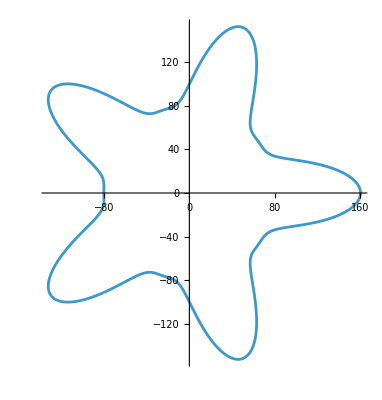

```mathematica
ParametricPlot[{r[θ]*Cos[θ],r[θ]*Sin[θ]},{θ,0,2*π}]
```

## Square

```mathematica
a=160;
```

```mathematica
r[θ_]:=a/Max[Abs[Cos[θ]],Abs[Sin[θ]]]
```

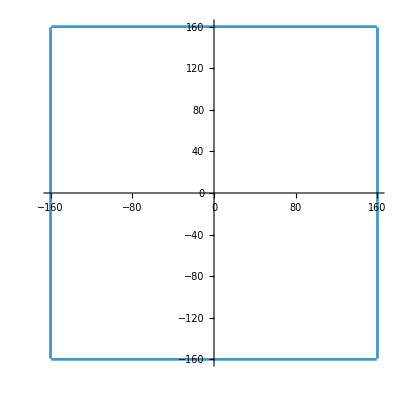

```mathematica
ParametricPlot[{r[θ]*Cos[θ],r[θ]*Sin[θ]},{θ,0,2*π}]
```